```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/chains/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/chains

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
intrachainAvail=Normal[DeleteDuplicates[ds[Take,"intrachain"]]];
isotropyAvail=Normal[DeleteDuplicates[ds[Take,"isotropy"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail,"intrachain"->intrachainAvail,"isotropy"->isotropyAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,n_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];

Return[Table[{x[[i]],y[[i]]/y[[sizeAvail[[1]]]]},{i,Length[x]}]]
)
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[MaTeX,Magnification->2];

fs=22;
tckn=0.005;

plt=ListPlot[Log[10,spc],
SetOptions[LogTicks,TickLengthScale->1.5];
ImageSize->360,
Joined->False,
PlotMarkers->Automatic,
PlotStyle->If[aa==0.0,
Blue,
Purple
],
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
(*InterpolationOrder->0,*)
PlotRange->Log[10,{{10^-12,1},{10^-12,1}}],
PlotRangeClipping->True,
(*PlotLegends->Placed[Automatic,Right],*)
ClippingStyle->Automatic,
AspectRatio->0.85,
FrameLabel->MaTeX@{"J_{\\perp}","c_3 / c_0"},
Epilog->
{If[aa==1.0,
Inset[
MaTeX["\\alpha = 1"],
Scaled[{0.85,0.1}]],
Inset[
MaTeX["\\alpha = 0"],
Scaled[{0.85,0.1}]]
]
},
(*ScalingFunctions->{"Log","Log"},*)
(*FrameTicks->{LinTicks[0,1,0.5,5],LinTicks[0,1,0.5,5,ShowTickLabels->False],LinTicks[-3,3,1,1],LinTicks[-3,3,1,1,ShowTickLabels->False]}*)
FrameTicks->{{LogTicks[-12,0,TickLabelStep->4,ShowMinorTicks->False],LogTicks[-12,0,TickLabelStep->4,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[-12,0,TickLabelStep->4,ShowMinorTicks->False],LogTicks[-12,0,TickLabelStep->4,ShowTickLabels->False,ShowMinorTicks->False]}}
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#coupling==J&&#intrachain==KK&&#isotropy==aa&]};
keys={"magnons","coefficients"};

plots={};
Do[(
Do[(
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys,n];
AppendTo[buff,{KK,-Log[10,spc[[-1,2]]]}];
),{KK,spcAvail["intrachain"]//Normal}];
AppendTo[plots,getDPlot[buff,n]];
),{aa,spcAvail["isotropy"]//Normal}];
),{J,spcAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
tails={"[10^-12,10^-11,10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,10^-3,10^-2,10^-1]_[0.0,1.0]"};
head = "mc";
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[head,JRange,tail]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{tail,tails}]
```

```mathematica
spcAvail
```

```mathematica
Grid[Reverse[spcPlots[[1]],2]]
(*Grid[Reverse[spcPlots[[2]],2]]*)
```

Grid[{-Graphics-,-Graphics-}]

```mathematica
SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head<>"r","/",
head<>"r","_L=",ToString[spcAvail["size"][[iN]]],
"_J=",ToString[spcAvail["coupling"][[iJ]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,spcPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iJ,Length[spcAvail["coupling"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)
```

```mathematica
(*SavePlots[]*)
```

```mathematica
(*fs=22;
SetOptions[MaTeX,Magnification->1.75];
pltjoint=Legended[Show[Reverse[spcPlots[[1,;;,2]]],PlotRange->{{0,3},{0,1}},
FrameTicks->{LinTicks[-3,3,1,1],LinTicks[0,1,0.5,5],LinTicks[-3,3,1,1,ShowTickLabels->False],LinTicks[0,1,0.5,5,ShowTickLabels->False]},
Epilog->{
Inset[MaTeX["\\alpha = 0"],Scaled[{0.15, 0.1}]]
}
],
Placed[PointLegend[{Orange,Purple,Lighter[Blend[{Red,Purple},0.75]],Lighter[Blend[{Red,Purple},0.25]]},
MaTeX@Reverse[{"J_{\\perp} = 1.0","J_{\\perp} = 0.1","J_{\\perp} = 0.01","J_{\\perp} = 10^{-12} \\approx 0"}],
LegendMarkerSize->16,Spacings->0.0,
LegendMarkers->{{"●",10},{"■",13},{"▼",12},{"▲",12}}],
Right]
]*)
```

```mathematica
Export["plots/c3_0.png",spcPlots[[1,1]],ImageResolution->300]
```

plots/c3_0.png

```mathematica
Export["plots/c3_1.png",spcPlots[[1,2]],ImageResolution->300]
```

plots/c3_1.png

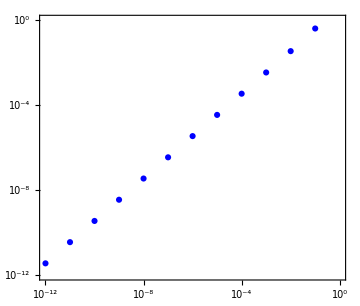
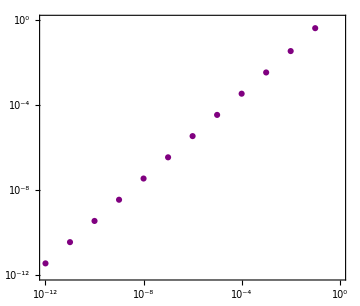

```mathematica
spcPlots
```

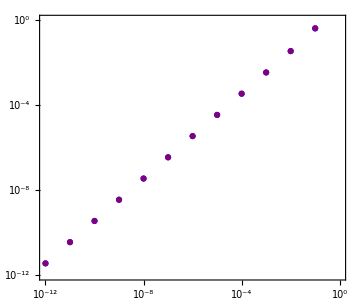

```mathematica
Show[spcPlots[[1]]]
```

```mathematica
spcDataset
```

```mathematica
-Log[10,0.006766/0.017569]
```

0.414415

```mathematica
-Log[10,0.0062378/0.0167688]
```

0.429471